# MATH7501 Practical 1, Semester1 -2021

## Topic: Basic Mathematica Usage

Author: Aminath Shausan
Date: 26-02-2021

## Pre-Tutorial Activity

Students must have downloaded Wolfram Mathematica following the link provided on MATH7501 Blackboard page

## Plan

Understand how to format cells in Wolfram Notebook

Learn three main methods to enter calculations

Learn how to compute basic calculations

Learn how to plot basic graphs

Learn how to produce interactive models

## How this Tutorial will Run

Tutor demonstrations

Student tasks to complete during the tutorial

## Mathematica Notebook Formatting & Styling

### 1) What is Mathematica?

Mathematica integrates symbolic and numerical calculations , graphics and visualization , programming , documentation , and dynamic interactivity into one big ensemble

It is used in many fields, including  science, engineering, mathematics, computing, and data science

Mathematica uses Wolfram Language

### 2) What is a Wolfram Notebook?

(Task) Open a New Notebook in Mathematica

A Wolfram notebook allows you to organise everything you do in Mathematica in a structured document including texts, executable codes, dynamic graphics, user interfaces, and more

Notice a blinking cursor. You can start typing right away. Notice the bracket that appears along the right side of the notebook in line with what you just typed. This bracket shows the extent of the cell

Cells are the basic structures of a Wolfram notebook.

Rule: use 'Shif+Enter' to evaluate content of an Input cell.

### 3) Three Main Methods to Format a Text Cell

Method 1: using the  cell insertion assistant (Click ‘+‘ sign  on the courser  > Other Style of Text)
Method 2: using the Menu bar (Format > Style )
Method 3: using keyboard shortcuts (‘Command/Alt + number',  number = 1, to 9)

(Task) Create a Title cell using cell insertion assistant. Type "MATH7501, Prac 1, Sem 1-2021"

(Task) Create a Subtitle cell  using Menu bar. Type "Basic Mathematica Usage"

(Task) Create a Section cell using Keyboard shortcut ( Command/Alt+5').  Type "Section 1: Entering Calculations"

(Task) Create a Subsection cell.   Type "1.1: Free-Form Input"

(Task) Create a Subsection cell.   Type "1.2: wolfram Language"

(Task) Create a Subsection cell.   Type "1.3: Palette"

## 1. Entering Calculations

### 1.1 Free-Form Input

lets you enter commands using plain English language

To create a Free-Form Input cell,

click  ‘=’ sign on keyboard Or

Cell Insertion assistant (Click ‘+‘ sign courser on the left of a new cell > Free-Form Input )

(Task) Type "graph  y = 3 x - 7" . Press Shift+ Enter

WolframAlphaQueryParseResults

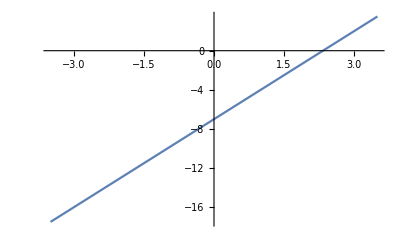

### 1.2 Wolfram Language

gives you flexibility and power to tell Mathematica exactly what you wanted to do

Rule 1: Capital letters to start all function names

Rule 2: Function arguments are enclosed by square brackets [ ]

Rule 3: Lists, ranges, and domains are enclosed by curly braces { }

Rule 4: To suppress output, use a semicolon , ‘;’

(Task) Plot  y = 3 x - 7  from -3 to +3

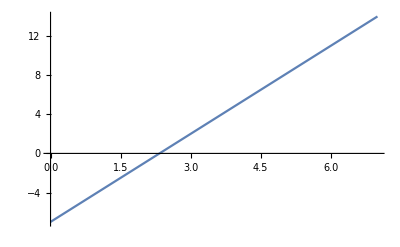

```mathematica
Plot[ 3 x -7,{x, 0, 7}]
```

To get  help for built-in functions: use any of the following methods

go to Menu bar (Help > Find Selected Functions)

type '? + name of function'

click the double chevron which appears, when you put mouse cursor,  on the function name

```mathematica
?Plot
```

### 1.3 Palettes

An alternate way to enter calculations

(Task) Plot  y = 3 x - 7  from -3 to +3   (Palettes > Basic Math Assistant > Basic Commands > 2D > Plot)

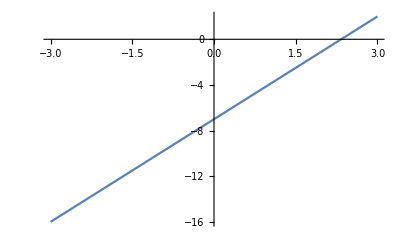

```mathematica
Plot[3x -7,{x,-3,+3}]
```

## 2. Basic Calculations

### 2.1 Numerical Output

Mathematica always gives you exact result where possible for numerical calculations

If you want numerical approximation, use numerical approximation function N[ ] or the suggestion bar option, or enter numerical values with a dot

(Task) calculate numeric approximation of  1/(√(2 π)).

(To enter √■ , use  Palettes > Basic Math Assistant >  Typesetting (or Calculator) OR keyboard shortcut ‘Ctrl + 2’)

(To enter π , use  Palettes > Basic Math Assistant >  Typesetting (or Calculator) OR keyboard shortcut ‘Esc + p +Esc’)

```mathematica
1/(√(2π))
```

1/(√(2 π))

```mathematica
N[1/(√(2 π)),3]
```

0.399

```mathematica
1.0/(√(2π))
```

0.398942

### 2.2 Variable Assignments (use ‘=’ sign)

Mathematica can be used to evaluate expressions

If a variable is not previously assigned a value, it is shown in blue color. Once a value is give for it, then Wolfram Language keeps it in memory and usually assumes that it is assigned globally. This means that every time you use the variable, the Wolfram Language assumes that you are referring to the same object.

Use Clear[ ] function to clear the value assigned to a given variable from memory

However, you may not want all your variables to be global. Sometimes, you may wish to name the letter y to refer to two different variables in two different programs. In this case you are required to use y in each program as a local variable. The Module[ ] function (see below) can be used in this case.

(Task) evaluate 3a+1 for a = 3

```mathematica
a = 2;
3 a + 1
```

7

```mathematica
Clear[a]
```

### 2.3 Substitution (use ‘/.’ sign)

(Task) Substitute a = 3 in 3a+1

```mathematica
3 a + 1 /. a -> 2
```

7

### 2.4 Integrate and Simplify

(Task) Integrate cos (2x) and simplify the result

```mathematica
Integrate[Cos[2 x],x]
```

1/2 Sin[2 x]

```mathematica
Simplify[1/2 Sin[2 x]]
```

Cos[x] Sin[x]

### 2.5 Solving equations (use ‘==’ sign)

(Task) solve 3y+12 =0

```mathematica
Solve[3 y +12 ==0, y]
```

{{y→-4}}

### 2.6 Defining Functions (use ‘f[var1_,var2_,...]:=’)

(Task) Suppose f(x, y) = x^2+y^2. Find f(2,2) . (To enter superscript 2 use ‘Control + 6’ OR ‘Insert > Typesettining)

```mathematica
f[x_,y_]:= x^2+y^2;
```

```mathematica
f[2,2]
```

8

```mathematica
Clear[f]
```

### 2.7 Create Own Function with Local variables (use Module [ ])

(Task) Create a function to solve x^2= n, for various integer values of n

```mathematica
myFunc[n_]:= Module[{a},a = n; Solve[x^2==a, x]]
```

```mathematica
myFunc[3]
```

{{x→-√3},{x→√3}}

(Task) create a function to add  n integers from 1 to n

```mathematica
myFunc[n_]:=Module[{k},Sum[k,{k,1,n}]]
```

## 3. Basic Graphics

(Task)   plot sin(x) from -2π to 2π

change the domain from 0 to π

label the graph,

(Task)  plot sin(x^2+y^2) for x between -3 to 3, and y between -3 to 3

(Task) create a 3D graph of sin(x y) , x, y between -π to + π

## 4. Interactive Models

Interactive plots allow you to visualise changes to a plot when variables are varied

To create an interactive model use Manipulate[ ] function

(Task) Visualise sin(frequency  x ) as frequency varies from 1 to 5

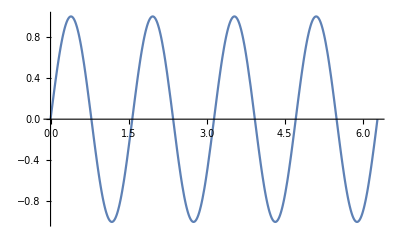

```mathematica
Plot[Sin[4 x],{x, 0,2π }]
```

```mathematica
Manipulate[Plot[Sin[frequency*x],{x, 0, 2π}],{frequency, 1, 5}]
```

(Task) Visualise sin(frequency x ) , cos(frequency x ) , tan(frequency x ) as as both frequency and trig functions varies

```mathematica
Manipulate[Plot[function[frequency*x],{x, 0, 2π}],{frequency, 1, 5},{function,{Sin, Cos, Tan}}]
```

(Task) visualise expansion of (y + (z))^n for n from 1 to 100 in steps 1

## 5. Matrices

### 5.1 Three Methods to Create a Matrix

#### By Typing (crate a list of lists list {{a, b, c}, {d, e, f}} and MatrixForm)

(Task) Create a matrix with 2 rows and 3 columns

```mathematica
A = {{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
A// MatrixForm
```

(a | b
c | d)

#### Using Keyboard Shortcuts

Use ‘Ctrl + ,’ to add a column

Use ‘Ctrl + Enter’ to add a row

```mathematica
({{a, b}, {c, d}})
```

#### Using Table [ ] Function

From Menu bar select Insert > Table/Matrix > New

```mathematica
({{a, b}, {c, d}})
```

### 5.2 Determinant (Use Det [ ] Function)

(Task) Compute general formula for determinant of a 2 by 2 matrix

```mathematica
Det[A]
```

-b c+a d

### 5.3 Inverse (Use Inverse[ ] Function)

(Task) Compute general formula for inverse  of a 2 by 2 matrix

```mathematica
Inverse[A]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

## 6. Classic Programming

(Task) Use   Do[ ], For[ ], and While[ ] loops to print the first four square numbers

### 6.1 Do[ ] Loop

```mathematica
Do[Print[n^2],{n,1,4}]
```

1

4

9

16

### 6.1 For[ ] Loop

```mathematica
For[n=1,n<5, n++, Print[n^2]]
```

1

4

9

16

### 6.1 While[ ] Loop

```mathematica
n =1;
While[n<5, Print[n^2]; n++]
```

1

4

9

16

## 7. More Resources

Help > Wolfram Documentation  (or https://reference.wolfram.com/language/)

Mathematica based exercises,  link provided in MATH7501 course website

Dr Sam Hambleton YouTube tutorials, link provided in MATH7501 course website